```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub716p5/buffer/fpi.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p5/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p5=Transpose[{Log[t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
(*fpi=Flatten[Import["./LPA_Tscaling_mub716p6/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p6/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p6=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p66/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p66/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p66=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p6608/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p6608/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p6608=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./LPA_Tscaling_mub716p66084/buffer/mSigma.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p66084/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p66084=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];*)
fpi=Flatten[Import["./LPA_Tscaling_mub716p661/buffer/fpi.dat"]];
T=Flatten[Import["./LPA_Tscaling_mub716p661/buffer/TMeV.dat"]];
t=-(T-T[[1]])/T[[1]];
data=Transpose[{Log[t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub716p661=Transpose[{Log[t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

## Plot

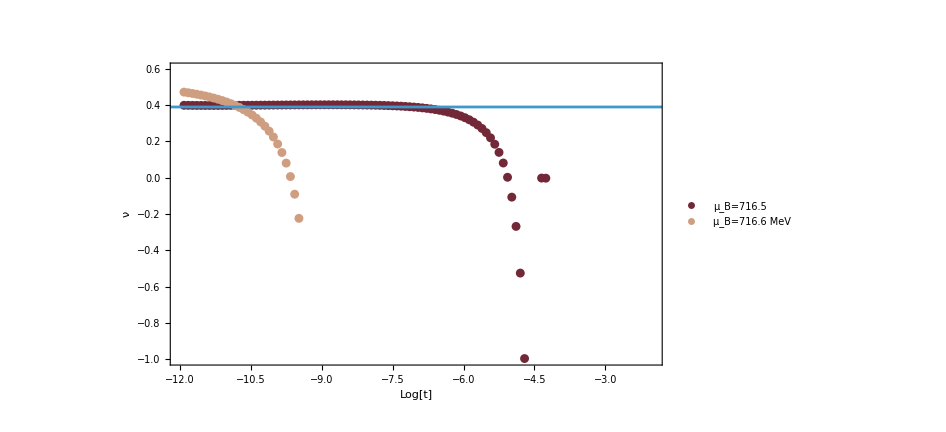

```mathematica
plotT=Show[ListPlot[{(*b1mub0,b1mub50,b1mub100,b1mub150,b1mub200,b1mub250,b1mub300,b1mub350,b1mub400,b1mub450,b1mub500,b1mub550,b1mub600,b1mub650,b1mub700,(*b1mub703,*)(*b1mub705,*)b1mub707,b1mub710,b1mub715,*)b1mub716p5(*,b1mub716p6,b1mub716p66,b1mub716p6608,b1mub716p66084*),b1mub716p661},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.3}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=716.5","μ_B=716.6 MeV","μ_B=716.66 MeV","μ_B=716.6608 MeV","μ_B=716.66084 MeV","μ_B=716.661 MeV","μ_B=300 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.7}],
PlotRange->{{-12,-2},{-1.,0.6}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.39},{10,0.39}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```